```mathematica
Quiet[Remove["Global`*"],{Remove::rmnsm}];Print["Mathematica $Version = “",$Version,"”"];Print["Execution time = ",DateString[DateList[],{"Hour",":","Minute"," on ","DayNameShort"," ","Day"," ","MonthNameShort"," ","Year"}]];
```

Mathematica $Version = “9.0 for Mac OS X x86 (64-bit) (January 24, 2013)”

Execution time = 17:30 on Mon 02 Jan 2023

```mathematica
simplifyExtra:=Simplify[PowerExpand[Simplify[#]]]&;
```

```mathematica
KnotsFromCoeffs[{c0_:0,c1_:0,c2_:0,c3_:0}]={c0,c0+c1/3,c0+(2c1+c2)/3,c0+c1+c2+c3};
CoeffsFromKnots[{z0_,z1_,z2_,z3_}]=PadRight[{z0,-3 z0+3 z1,3 z0-6 z1+3 z2,-z0+3 z1-3 z2+z3},4];
CoeffsBezierSplit[coeffs_List,t0_,t1_]:=Module[{t},(PadRight[CoefficientList[Table[(t0*(1-t)+t1*t)^i,{i,0,3}].PadRight[coeffs,4,0],t],4,0])//simplifyExtra];
KnotsBezierSplit[{z0_,z1_,z2_,z3_},t0_,t1_]:=KnotsFromCoeffs[CoeffsBezierSplit[CoeffsFromKnots[{z0,z1,z2,z3}],t0,t1]]//simplifyExtra;
```

```mathematica
(* For a 90° arc, Adobe Distiller hardcodes a speed of 0.552; GhostScript’s speed ≈ 0.552284 which might be (Sqrt[2] - 1)4/3 *)
(* Boolean: True = Adobe; False = GhostScript *)
knots=({{0, z, 1-z, 1}, {0, 0, 1, 1}});
```

```mathematica
x=CoeffsFromKnots[knots⟦1⟧].{1,t,t^2,t^3};
y=CoeffsFromKnots[knots⟦2⟧].{1,t,t^2,t^3};
```

```mathematica
D[x,t]/D[y,t]/.{t->1/2}//Simplify
```

1-z

```mathematica
z=8/10;  (* Aesthetic judgement. 1 would be vertical; 0.8 looks good. *)
```

```mathematica
{x,y}
```

{(12 t)/5-(21 t^2)/5+(14 t^3)/5,3 t^2-2 t^3}

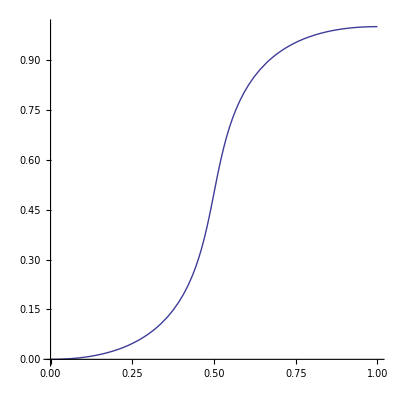

```mathematica
ParametricPlot[{x,y},{t,0,1}]
```

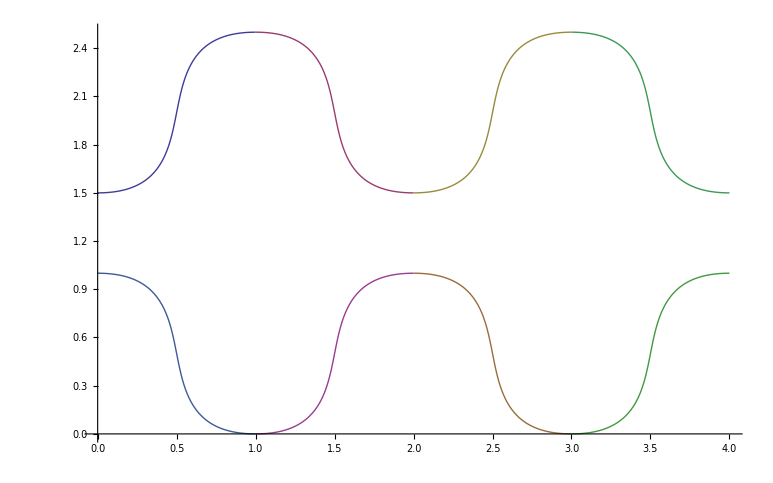

```mathematica
ParametricPlot[{{x,1.5+y},{x+1,2.5-y},{x+2,1.5+y},{x+3,2.5-y},{x,1-y},{x+1,y},{x+2,1-y},{x+3,y}},{t,0,1}]
```